```mathematica
(*1*)
(*через встроенные функции*)
```

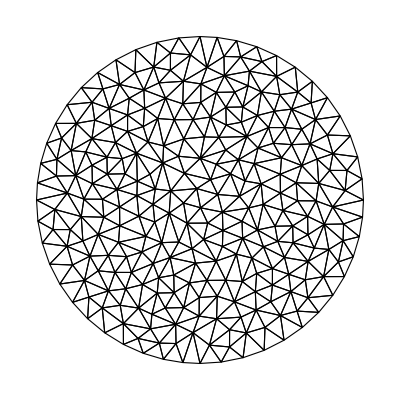

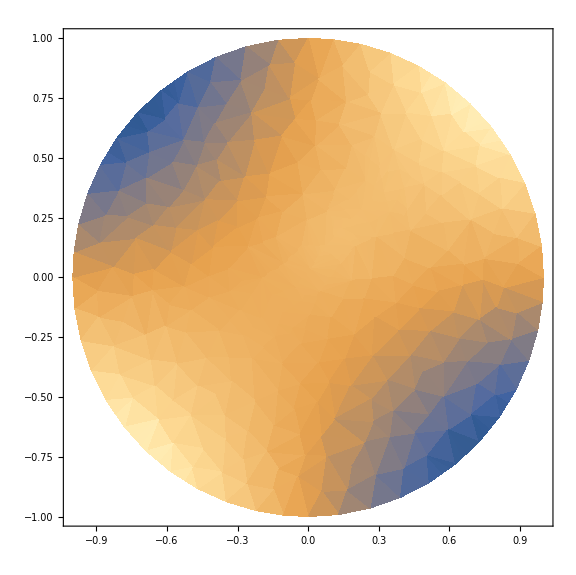

```mathematica
Clear["Global`*"]
Needs["NDSolve`FEM`"]
Ω=ImplicitRegion[x^2+y^2≤1,{x,y}];
mesh=ToElementMesh[Ω,MaxCellMeasure->0.01];
mesh["Wireframe"]

xc=0.1;
yc=0.15;
σ=0.1;

gauss[x_,y_]=PDF[NormalDistribution[xc,σ]][x]*PDF[NormalDistribution[yc,σ]][y];
op=-Laplacian[u[x,y],{x,y}]-gauss[x,y];

Γ=DirichletCondition[u[x,y]==2*x*y, x^2+y^2==1];
sol=NDSolveValue[{op==0,Γ},u[x,y],{x,y}∈mesh];
Show[
DensityPlot[sol,{x,y}∈mesh,AspectRatio->Automatic,ImageSize->Large](*,
mesh["Wireframe"]*)]
```

```mathematica
(*вручную*)
```

```mathematica
Clear["Global`*"]
Needs["NDSolve`FEM`"]
Ω=ImplicitRegion[x^2+y^2≤1,{x,y}];
mesh=DiscretizeRegion[Ω];
coord=MeshCoordinates[mesh];
cells=MeshCells[mesh,2];
primitives=MeshPrimitives[mesh,2];
```

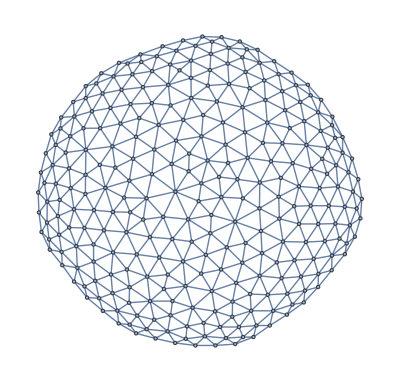

```mathematica
(*составляем матрицу смежности*)
cm=mesh["ConnectivityMatrix"[0,1]].mesh["ConnectivityMatrix"[1,0]];
nzp=cm["NonzeroPositions"];
nzp=Select[nzp,#[[1]]≠#[[2]]&];
cm=Normal[SparseArray[nzp->Table[1,Dimensions[nzp][[1]]]]];
AdjacencyGraph[cm]
```

```mathematica
(*разбираемся с матрицей смежности*)
cm2=mesh["ConnectivityMatrix"[0,1]].mesh["ConnectivityMatrix"[1,0]];
nzp2=cm2["NonzeroPositions"];
(*nzp2=Select[nzp2,#[[1]]≠#[[2]]&];*)
cm2=Normal[SparseArray[nzp2->Table[1,Dimensions[nzp2][[1]]]]];
f[a_]:=MeshPrimitives[mesh,0][[a]];
Graphics[Map[f,Position[cm2[[200]],1]]]

cm02=mesh["ConnectivityMatrix"[0,2]];
nzp02=cm02["NonzeroPositions"];
cm02=Normal[SparseArray[nzp02->Table[1,Dimensions[nzp02][[1]]]]];

f[a_]:=MeshPrimitives[mesh,2][[a]];
Map[f,Position[cm02[[276,All]],1],1]
EdgeList[AdjacencyGraph[cm]];
```

-Graphics-

{{Polygon[{{-0.791903,0.187774},{-0.772055,0.276779},{-0.862205,0.260506}}]},{Polygon[{{-0.68611,0.307262},{-0.806545,0.361197},{-0.772055,0.276779}}]},{Polygon[{{-0.772055,0.276779},{-0.69267,0.16815},{-0.68611,0.307262}}]},{Polygon[{{-0.862205,0.260506},{-0.772055,0.276779},{-0.806545,0.361197}}]},{Polygon[{{-0.69267,0.16815},{-0.772055,0.276779},{-0.791903,0.187774}}]}}

```mathematica
(*Без connectivity matrix*)
Clear[basisFunc];
basisFunc={};
Clear[bFlist];
bFlist={};
basisFunc={};
Clear[regs];
regs={};
temp=Reap[For[i=1,i≤MeshCellCount[mesh,0],i++,
poly=Select[cells,MemberQ[#[[1]],i]&];
polyCoord=Sow[poly/.Polygon[a__]:>Polygon@coord[[a]],mR];
(*MeshRegion[coord,poly];*)
(*уравнение плоскости через три точки det({{x-x1, y-y1, z-z1}, {x1-x2, y1-y2, z1-z2}, {x1-x3, y1-y3, y1-y3}})=0*)
Clear[f];
f={};
versh[index_,pos_,pol_]:=If[pol[[1,pos]]==index,1,0];
f=Sow[Reap[For[j=1,j<=Length[polyCoord],j++,

r1={x1,y1,versh[i,1,poly[[j]]]};
r2={x2,y2,versh[i,2,poly[[j]]]};
r3={x3,y3,versh[i,3,poly[[j]]]};
r={x,y,z};
solz=Solve[(Cross[r1-r2,r1-r3]).(r-r1)==0,z];
Sow[{(z/.solz/.{Map[#[[1]]->#[[2]]&,Transpose[{Flatten[{{x1,y1},{x2,y2},{x3,y3}}],Flatten[polyCoord[[j,1]]]}]]})[[1,1]],{x,y}∈polyCoord[[j]]}];
]][[2,1]],mF];
]][[2]];
basisFunc=Piecewise/@temp[[2]];
bFlist=temp[[2]];
```

```mathematica
(*regs=RegionUnion/@temp[[1]];*)
```

```mathematica
(*считаем интегралы перекрытия для случая одинаковых пирамидок*)
integi1i2[ind1_,ind2_]:=
If[ind1==ind2,
{integInd1Ind2=0;
For[polyCount=1,polyCount<=Length[bFlist[[ind1]]],polyCount++,
integInd1Ind2=integInd1Ind2+NIntegrate[bFlist[[ind1]][[polyCount,1]]*bFlist[[ind1]][[polyCount,1]],bFlist[[ind1]][[polyCount,2]],Method->{Automatic,"SymbolicProcessing"->0}];
];
integInd1Ind2},
(*считаем интегралы перекрытия для случая неодинаковых пирамидок*)
{temp=Flatten[{bFlist[[ind1]],
bFlist[[ind2]]},2];(*переменная в которой будет храниться функция и ее область определения как равноправные элементы одного массива, причем собираем в нее две функции*)
intersecInd1Ind2=Tally[temp];(*ищем полигоны, по которым пересекаются функции(пирамидки)*)
intersecInd1Ind2=Select[intersecInd1Ind2,Part[#,2]>1&][[All,1]];(*Запоминаем полигоны, по которым есть пересечение*)
integInd1Ind2=0;(*интеграл перекрыти функций*)
For[interCount=1,interCount≤Length[intersecInd1Ind2],interCount++,
{interFunc=Flatten[Position[temp,intersecInd1Ind2[[interCount]]]]-1;(*находим функции, которые нужно интегрировать(они стоят на позицию раньше соответствующего полигона)*)
integInd1Ind2=integInd1Ind2+NIntegrate[temp[[interFunc[[1]]]]*temp[[interFunc[[2]]]],intersecInd1Ind2[[interCount]],Method->{Automatic,"SymbolicProcessing"->0}];}
];
integInd1Ind2}][[1]];
```

```mathematica
(gMatix=-ParallelTable[integi1i2[i1,i2],{i1,1,Length[bFlist]},{i2,1,Length[bFlist]}])//AbsoluteTiming
```

{109.738,{1}}
 |  |  |  |

```mathematica
(*считаем интегралы перекрытия градиентов для случая одинаковых пирамидок*)
integDi1Di2[ind1_,ind2_]:=
If[ind1==ind2,
{integInd1Ind2=0;
For[polyCount=1,polyCount<=Length[bFlist[[ind1]]],polyCount++,
integInd1Ind2=integInd1Ind2+Grad[bFlist[[ind1]][[polyCount,1]],{x,y}].Grad[bFlist[[ind1]][[polyCount,1]],{x,y}]*RegionMeasure[bFlist[[ind1]][[polyCount,2]]/.{x,y}∈Polygon[a__]->Polygon[a]];
];
integInd1Ind2},
(*считаем интегралы перекрытия градиентов для случая неодинаковых пирамидок*)
{temp=Flatten[{bFlist[[ind1]],
bFlist[[ind2]]},2];(*переменная в которой будет храниться функция и ее область определения как равноправные элементы одного массива, причем собираем в нее две функции*)
intersecInd1Ind2=Tally[temp];(*ищем полигоны, по которым пересекаются функции(пирамидки)*)
intersecInd1Ind2=Select[intersecInd1Ind2,Part[#,2]>1&][[All,1]];(*Запоминаем полигоны, по которым есть пересечение*)
integInd1Ind2=0;(*интеграл перекрыти функций*)
For[interCount=1,interCount≤Length[intersecInd1Ind2],interCount++,
{interFunc=Flatten[Position[temp,intersecInd1Ind2[[interCount]]]]-1;(*находим функции, которые нужно интегрировать(они стоят на позицию раньше соответствующего полигона)*)
integInd1Ind2=integInd1Ind2+Grad[temp[[interFunc[[1]]]],{x,y}].Grad[temp[[interFunc[[2]]]],{x,y}]*RegionMeasure[intersecInd1Ind2[[interCount]]/.{x,y}∈Polygon[a__]->Polygon[a]];}
];
integInd1Ind2}][[1]];
Timing[kMatrix=ParallelTable[integDi1Di2[i1,i2],{i1,1,Length[bFlist]},{i2,1,Length[bFlist]}]][[1]]
```

0.205632

```mathematica
kMatrix[[1,1]]
```

1.9302

```mathematica
xc=0.1;
yc=0.15;
σ=0.1;

gauss[x_,y_]=PDF[NormalDistribution[xc,σ]][x]*PDF[NormalDistribution[yc,σ]][y];
razl[func_,ind_]:=Sum[NIntegrate[func[x,y]*bFlist[[ind,counter,1]],bFlist[[ind,counter,2]],Method->{Automatic,"SymbolicProcessing"->0}],{counter,1,Length[bFlist[[ind]]]}];

g=ParallelTable[razl[gauss,i],{i,1,Length[bFlist]}];
gcoeff=LinearSolve[gMatix,g];
points=MeshPrimitives[mesh,0]/.Point[a__]->a;
points=Transpose[AppendTo[Transpose[points],gcoeff]];
ListPlot3D[points,PlotRange->All,ImageSize->Large]
```

-Graphics3D-

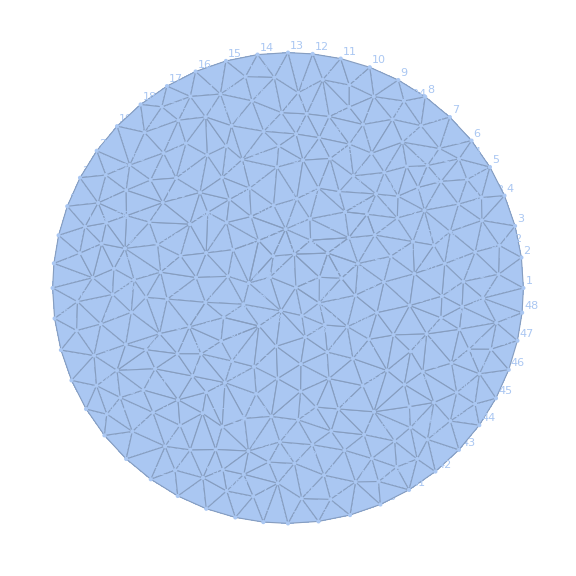

48

```mathematica
(*находим граничные полигоны*)
HighlightMesh[mesh, Labeled[0,"Index"],ImageSize->Large]
MeshCellCount[BoundaryMesh[mesh],1]
```

```mathematica
(*составляем функционал и минимизируем его*)
coeffs=Table[Subscript[c,n],{n,1,Length[bFlist]}];
Table[coeffs[[i]]=2*coord[[i,1]]*coord[[i,2]],{i,1,MeshCellCount[BoundaryMesh[mesh],1]}];
func=coeffs.kMatrix.coeffs-2*coeffs.gMatix.gcoeff;

sol=NMinimize[func,coeffs[[49;;]]][[2]];
```

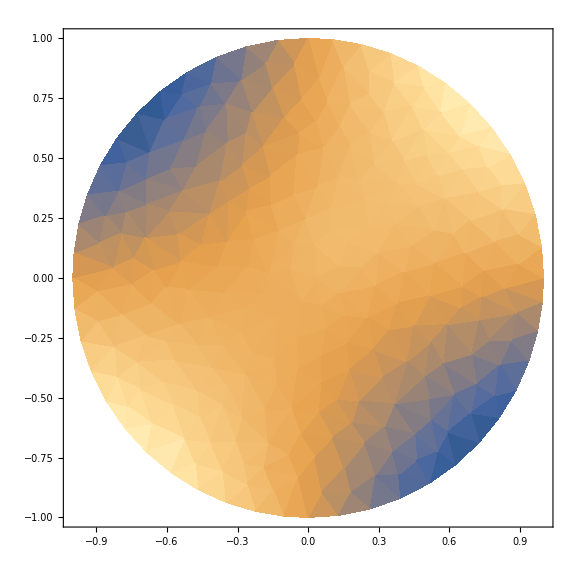

48

```mathematica
points=MeshPrimitives[mesh,0]/.Point[a__]->a;
finres=Transpose[AppendTo[Transpose[points],coeffs/.sol]];
ListDensityPlot[finres,PlotRange->All,ImageSize->Large]
```